```mathematica
Clear[t,II,D1,D2,S1,S2,D2,x1,x2,x3,Q1,Q2,G,UG,DD,u,v](*******************************************************************)
(* Задаем начальные условия *)
(*******************************************************************)
T=1400;
D10=7;
D20=13;
II0=0;
S10=0;
S20=0;
Q10=100;
Q20=20;
x10=0;
x20=0;
x30=0;
```

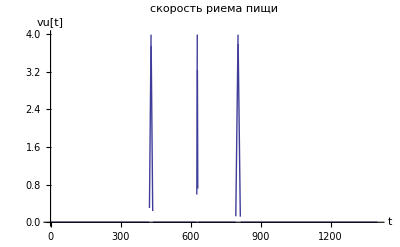

```mathematica
(*******************************************************************)
(* Задаем параметры для подсистемы приема пищи*)
(*******************************************************************)
(* моменты приема пищи *)
t1=423;
t2=626;
t3=793;
t4=1063;
t5=1325;
(* длительность приема пищи *)
d1=15;
d2=5;
d3=20;
d4=20;
d5=5;
(*масса принятой пищи *)
m1=30;
m2=10;
m3=40;
m4=40;
m5=10;

d[t_,a_,m_]:=Piecewise[{{4*m*t/a^2,0<=t<=a/2},{(4*m/a)-(4*m*t/a^2),a/2<t<=a},{0,t<0 || t>a}}];(*вспомогательная кусочно-постоянная функция *)
v[t_]=d[t-t1,d1,m1]+d[t-t2,d2,m2]+d[t-t3,d3,m3]+d[t-t4,d4,m4]+d[t-t5,d5,m5];(*поглощенная углеводная пища,g/min *)
Plot[v[t],{t,0,T},  AxesLabel->{t,"vu[t]"},PlotLabel->"скорость риема пищи"]
```

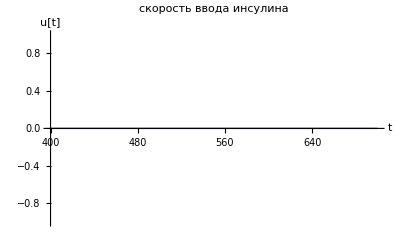

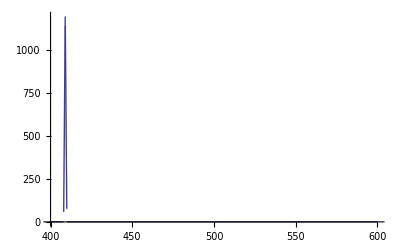

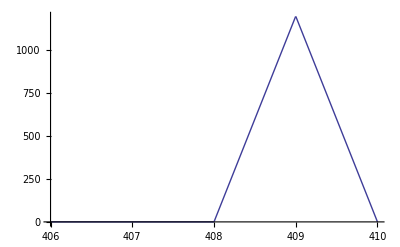

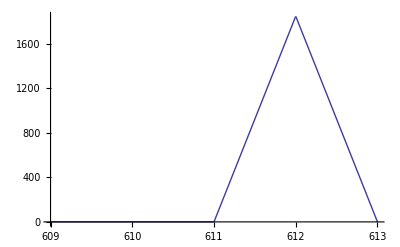

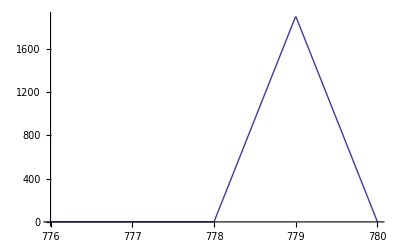

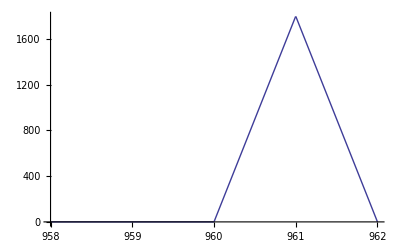

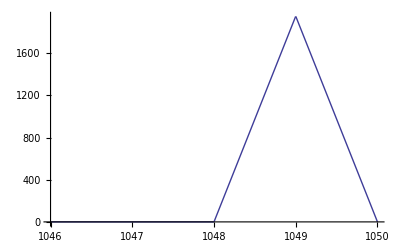

```mathematica
m=0; (* вариация мыссы инсулина*)
c=0; (* вариация времени вводи инсулина *)

it1=408+c;
it2=611+c;
it3=778+c;
it4=960+c;
it5=1048+c;
it6=1310+c;
(* длительность ввода инсулина*)
id1=2;
id2=2;
id3=2;
id4=2;
id5=2;
id6=2;
(*масса ввееденного инсулина*)
im1=1200+m;
im2=1850+m;
im3=1900+m;
im4=1800+m;
im5=1950+m;
im6=1890+m;
n[t_,b_,l_]:=Piecewise[{{4*l*t/b^2,0<=t<=b/2},{(4*l/b)-(4*l*t/b^2),b/2<t<=b},{0,t<0 || t>b}}];
u[t_]=n[t-it1,id1,im1]+n[t-it2,id2,im2]+n[t-it3,id3,im3]+n[t-it4,id4,im4]+n[t-it5,id5,im5]+n[t-it6,id6,im6];(*количество введённого инсулина- СКОРОСТЬ???????????????*)
Plot[u[t],{t,400,T/2},  AxesLabel->{t,"u[t]"},PlotLabel->"скорость ввода инсулина"]
U=Plot[u[t],{t,400,600}]
U1=Plot[u[t],{t,it1-2,it1+2}]
U2=Plot[u[t],{t,it2-2,it2+2}]
U3=Plot[u[t],{t,it3-2,it3+2}]
U4=Plot[u[t],{t,it4-2,it4+2}]
U5=Plot[u[t],{t,it5-2,it5+2}]
```

```mathematica
(*******************************************************************)
(*Задаем параметры подсистемы действия инсулина*)
(*******************************************************************)
VI=0.12*Bw;(*объём зоны,распределение инсулина, L*)
Ke =0.138;(*Скорость поглащения инсулина, 1/min*)
Bw=70 ;(*вес пациента, kg*)
tauS=55;(*время абсорции введенного инсулина, min*)
kb1=3.07*10^(-5);(*показатель транспортировки и распространения инсулина, L/(mU*min*)
kb2=4.92*10^(-5);(*показатель поглощения инсулина, L/(mU*min)*)
kb3=0.0016;(*показатель влияния инсулина на выработку глюкозы в печени, L/(mU*min)*)
ka1=0.0066;(*скорость деактивации транспортировки и распространения инсулина, 1/min*)
ka2=0.06;(*скорость деактивации поглощения инсулина, 1/min*)
ka3=0.03;(*скорость (деактивации) влияния инсулина на выработку глюкозы в печени, 1/min*)
(* моменты ввода инсулина *)
```

```mathematica
(*******************************************************************)
(* Задаем параметры для подсистемы образования глюкозы з углеводной пищи*)
(*******************************************************************)

AG=0.8;(* параметр биоактивности углеводов *)
tauD=40; (* время,в течение которого принятая пища войдет в кровеносные сосуды как глюкоза,   min *)
MwG=180 ;(* молекулярный вес глюкозы,  mmol*)
DD[t_]=1000v[t]/MwG;(*ввод углеводной пищи,  min/mmol   ???  преобразование пищи в глюкозу????  *)


(*******************************************************************)
(* Решаем систему уравнений подсистемы образования глюкозы *)
(*******************************************************************)
Clear[D1,D2]
SolD=NDSolve[{D1'[t]==AG DD[t]-D1[t]/tauD,
D2'[t]==(D1[t]-D2[t])/tauD,
D1[0]==D10,D2[0]==D20},{D1[t],D2[t]},{t,0,T}];
D1[t_]=SolD[[1,1,2]] ;(*массив -- извлекаем функцию из решения*)
D2[t_]=SolD[[1,2,2]];
```

```mathematica
(*******************************************************************)
(*Задаем параметры подсистемы распространения глюкозы в организме человека*)
(*******************************************************************)
VG=0.16*Bw;(*объем распределения глюкозы, L*)
f01=0.0097*Bw;(*скорость потребления глюкозы независимо от действия инсулина в центральной нервной системе, mmol/min*)
EGP0=0.0161*Bw;(*скорость производства печенью глюкозы при нулевом уровне инсулина, mmol/min*)
tauD=40; (* время,в течение которого принятая пища войдет в кровеносные сосуды как глюкоза,   min *)
k12=0.066;(*скорость переноса глюкозы из периферийных тканей в кровяной поток, 1/min*)
UI[t_]=S2[t]/tauS;(*скорость абсорции инсулина, mU/min, зависит от количество инсулина в периферийных тканях*) 

(*******************************************************************)
(* Определяем переменные  подсистемы инсулина*)
(*******************************************************************)
II[t_];(*концентрация инсулина в плазме крови, mU/L*)
S1[t_];(*количество инсулина в крови, mU*)
S2[t_];(*количество инсулина в периферийных тканях, mU*)
x1[t_];(*показатель влияния инсулина на транспортировку и распространение глюкозы*)
x2[t_];(*показатель влияния инсулина на утилизацию глюкозы*)
x3[t_];(*показатель действия инсулина на выработку эндогенной глюкозы в печени*)
(*******************************************************************)
(* Решаем систему уравнений подсистемы инсулина *)
(*******************************************************************)
Clear[S1,S2,II,x1,x2,x3]
SolS=NDSolve[{II'[t]==S2[t]/(tauS VI)- Ke*II[t],
S1'[t]==-(S1[t]/tauS)+ u[t],
S2'[t]==(S1[t]-S2[t])/tauS,
II[0]==II0,S1[0]==S10,S2[0]==S20},{II[t],S1[t],S2[t]},{t,0,T},MaxStepSize->0.1, MaxSteps->100000];
II[t_]=SolS[[1,1,2]] ;(*извлекаем функцию*)
S1[t_]=SolS[[1,2,2]];
S2[t_]=SolS[[1,3,2]];
Solx=NDSolve[{x1'[t]==-ka1*x1[t]+kb1*II[t],
x2'[t]==-ka2*x2[t]+kb2*II[t],
x3'[t]==-ka3*x3[t]+kb3*II[t],x1[0]==x10,x2[0]==x20,x3[0]==x30},
{x1[t],x2[t],x3[t]},{t,0,T},MaxStepSize->0.1, MaxSteps->100000];
x1[t_]=Solx[[1,1,2]] ;(*извлекаем функцию*)
x2[t_]=Solx[[1,2,2]];
x3[t_]=Solx[[1,3,2]];
UG[t_]=D2[t]/tauD;(*Скорость всасывания (абсорбции) глюкозы в кишечнике, mmol/min*)
```

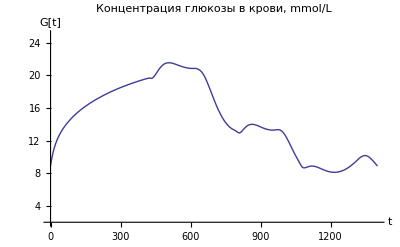

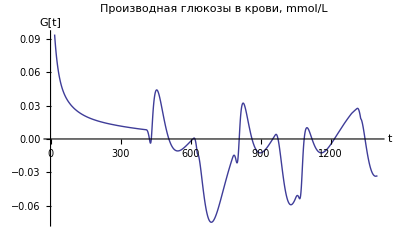

```mathematica
FR[t_]:=Piecewise[{{0.003(G[t]-9)*VG,G[t]>=9},{0,G[t]<9}}](* Скорость поглощения глюкозы в почках пациента, mmol/min *)
F01[t_]:=Piecewise[{{f01,G[t]>=4.5},{f01*G[t]/4.5,G[t]<4.5}} ](* Скорость потребления глюкозы в центральной нервной системе, mmol/min, f01 скорость потребления глюкозы независимо от действия инсулина*)
G[t_]:=Q1[t]/VG;(* концентрация глюкозы в крови пациента, mmol/L*)
Gp[t_]:=G'[t];


(*******************************************************************)
(* Определяем переменные распространения глюкозы в организме человека*)
(*******************************************************************)
Q1[t_];(* количество глюкозы в кровяном потоке, mmol *)
Q2[t_];(* количество глюкозы в периферийных тканях, 
mmol*)
(*******************************************************************)
(* Решаем систему уравнений, описывакющих распространения глюкозы в организме человека*)
(*******************************************************************)
Clear[Q1,Q2]
SolQ=NDSolve[{Q1'[t]==UG[t]−F01[t]−FR[t]−x1[t]*Q1[t]+k12*Q2[t]+EGP0(1−x3[t]),
 Q2'[t]==x1[t]*Q1[t]−(k12+x2[t])*Q2[t],Q1[0]==Q10,Q2[0]==Q20},{Q1[t],Q2[t]},{t,0,T},MaxStepSize->0.1, MaxSteps->100000];
Q1[t_]=SolQ[[1,1,2]]; 
Q2[t_]=SolQ[[1,2,2]];

Plot[G[t],{t,0,T},  AxesLabel->{t,"G[t]"},PlotLabel->"Концентрация глюкозы в крови, mmol/L",PlotRange->{2,25}]
Plot[Gp[t],{t,0,T},  AxesLabel->{t,"G[t]"},PlotLabel->"Производная глюкозы в крови, mmol/L"]
```

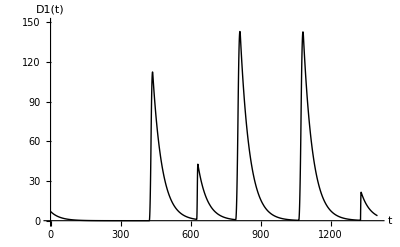

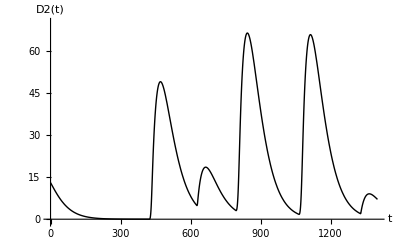

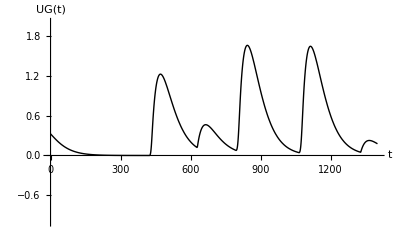

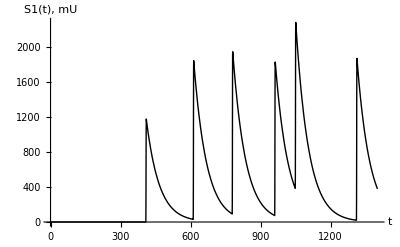

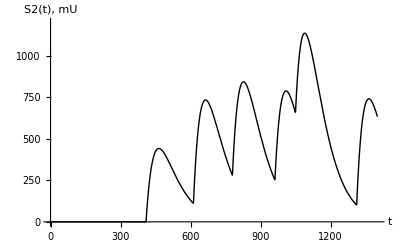

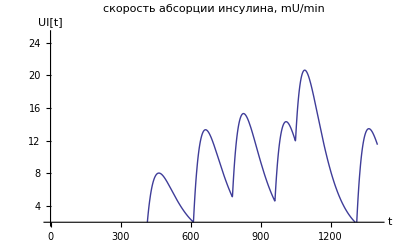

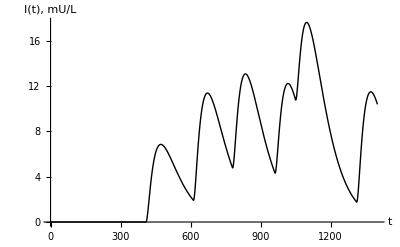

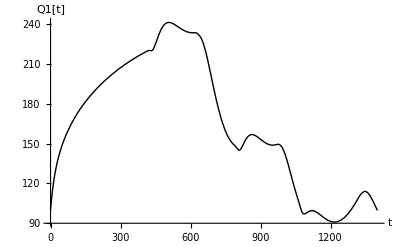

```mathematica
(* финальный вывод графиков *)
Plot[D1[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"D1(t)"},PlotRange->{-1,150}] 
Plot[D2[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"D2(t)"},PlotRange->{-1,70}]
Plot[UG[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"UG(t)"},PlotRange->{-1,2}]
Plot[S1[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"S1(t),  mU "}]
Plot[S2[t],{t,0,T},PlotRange->{-1,1200}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"S2(t), mU"}]

Plot[UI[t],{t,0,T},  AxesLabel->{t,"UI[t]"},PlotLabel->"скорость абсорции инсулина, mU/min",PlotRange->{2,25}]

Plot[II[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"I(t), mU/L"}]
Plot[Q1[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"Q1[t]"}]
Plot[Q2[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"Q2[t]"}]
Plot[x1[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"x1(t)"}]
Plot[x2[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"x2(t)"}]
Plot[x3[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"x3(t)"}]
Plot[G[t],{t,0,T}, PlotStyle->{Black,Thick}, LabelStyle->{Medium}, AxesLabel->{t,"G[t]"}]
```

```mathematica
a=1; (*коэффициент чувствительности к глюкозе*)
G0=5;
Gkr=10; (*критический уровень глюкозы*)
V=5;
Gint=NIntegrate[G[t]/1440,{t,0,1440}]
Iint=NIntegrate[II[t]/1440,{t,0,1440}]
delG=a*NIntegrate[(G[t]-Gkr)^2*V,{t,0,1440}]
delI=a*NIntegrate[(G[t]-Gkr)^2*V/5.5,{t,0,1440}]
```

14.5311

5.93529

288781.

52505.6

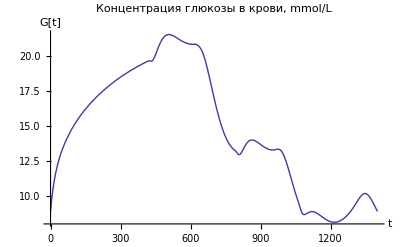

```mathematica
Plot[G[t],{t,0,T},  AxesLabel->{t,"G[t]"},PlotLabel->"Концентрация глюкозы в крови, mmol/L"]
```